g_μν=(-c^2 (1-(2 μ)/r) | 0 | -(2 a c μ)/r
0 | r^2/(a^2+r^2-2 r μ) | 0
-(2 a c μ)/r | 0 | a^2+r^2+(2 a^2 μ)/r)

g^μν=(-(r^3+a^2 (r+2 μ))/(c^2 r (a^2+r (r-2 μ))) | 0 | -(2 a μ)/(a^2 c r+c r^3-2 c r^2 μ)
0 | (a^2+r^2-2 r μ)/r^2 | 0
-(2 a μ)/(a^2 c r+c r^3-2 c r^2 μ) | 0 | (r-2 μ)/(a^2 r+r^3-2 r^2 μ))

dot{t}=(c k r^3-2 a h μ+a^2 c k (r+2 μ))/(c r (a^2+r (r-2 μ)))

dot{ϕ}=(h r-2 h μ+2 a c k μ)/(a^2 r+r^3-2 r^2 μ)

V_eff=(a^2 c^2+h^2-a^2 c^2 k^2)/(2 r^2)-(c^2 μ)/r+(-2 h^2 μ+4 a c h k μ-2 a^2 c^2 k^2 μ)/(2 r^3)

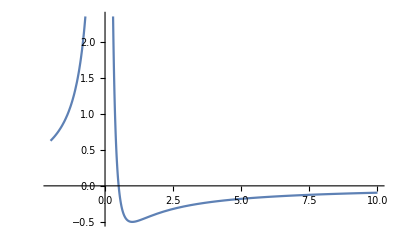

dV/dr=-(a^2 c^2+h^2-a^2 c^2 k^2)/r^3+(c^2 μ)/r^2-(3 (-2 h^2 μ+4 a c h k μ-2 a^2 c^2 k^2 μ))/(2 r^4)

sol1: r=a^2/(2 μ)+h^2/(2 c^2 μ)-(a^2 k^2)/(2 μ)-(√((-a^2 c^2-h^2+a^2 c^2 k^2)^2-4 c^2 μ (3 h^2 μ-6 a c h k μ+3 a^2 c^2 k^2 μ)))/(2 c^2 μ)

sol2: r=a^2/(2 μ)+h^2/(2 c^2 μ)-(a^2 k^2)/(2 μ)+(√((-a^2 c^2-h^2+a^2 c^2 k^2)^2-4 c^2 μ (3 h^2 μ-6 a c h k μ+3 a^2 c^2 k^2 μ)))/(2 c^2 μ)

V_eff=a c k u^2 X+1/2 u (a^2 c^2 u-2 c^2 μ)+1/2 u X^2 (u-2 u^2 μ)

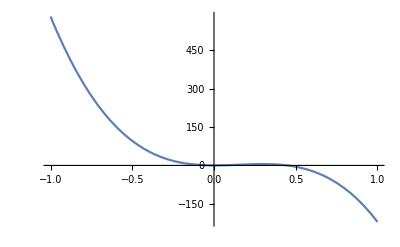

dV/du=u (a^2 c^2-a^2 c^2 k^2+(a c k+X)^2)-c^2 μ+3/2 u^2 (-2 a^2 c^2 k^2 μ+4 a c k (a c k+X) μ-2 (a c k+X)^2 μ)

D=a^2 c^2+2 a c k X+X^2 (1-12 c^2 μ^2)

sol1: u=1/(6 μ)+(a^2 c^2)/(6 X^2 μ)+(a c k)/(3 X μ)-(√((a^2 c^2+2 a c k X+X^2)^2-12 c^2 X^2 μ^2))/(6 X^2 μ)

sol2: u=1/(6 μ)+(a^2 c^2)/(6 X^2 μ)+(a c k)/(3 X μ)+(√((a^2 c^2+2 a c k X+X^2)^2-12 c^2 X^2 μ^2))/(6 X^2 μ)

```mathematica
Clear[h,x,V,k,r,ack];
x={t,r,ϕ};
g={{-c^2 (1-2μ/r),0,-2μ a c /r},{0,r^2/(r^2-2μ r+a^2),0},{-2μ a c /r,0,r^2 +a^2+2μ a ^2/r}};
Print["g_μν=",g//MatrixForm];
ginv=FullSimplify[Inverse[g]];
Print["g^μν=",ginv//MatrixForm];

Print["dot{t}=",Simplify[ginv[[1,1]]*(-k c^2)+ginv[[1,3]]*h]];
Print["dot{ϕ}=",Simplify[ginv[[3,1]]*(-k c^2)+ginv[[3,3]]*h]];

V=Collect[Simplify[(c^2+ginv[[1,1]]*(-k c^2)^2+ginv[[3,3]]*h^2+2ginv[[1,3]]*(-k c^2)*h+g[[2,2]]*dr^2)*((r^2+a^2-2 r μ)/(2 r^2))-dr^2/2+(c^2(k^2-1))/2],r];
Print["V_eff=",V];

Print[Plot[V/.{a->1,c->1,k->1,h->1,μ->1},{r,-2,10}]];

dV=D[V,r];
Print["dV/dr=",dV];
sol=Solve[{dV==0},r];

Print["sol1: r=",Expand[r/.sol[[1]]]];
Print["sol2: r=",Expand[r/.sol[[2]]]];

h=X+a c k;
r=1/u;

Print["V_eff=",Collect[Simplify[V],X]];

Print[Plot[V/.{a->1,c->1,k->1,X->-20,μ->1},{u,-1,1}]];

dV=D[V,u];
Print["dV/du=",dV];
sol=Solve[{dV==0},u];

dis=FullSimplify[Coefficient[dV,u]-4*Coefficient[dV,u^2]*(dV/.u->0)];
Print["D=",dis];

Print["sol1: u=",Expand[u/.sol[[1]]]];
Print["sol2: u=",Expand[u/.sol[[2]]]];
```